## EWS for stationary simulations of the Ricker model (no seasonality)

## Import data

```mathematica
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

### EWS data

```mathematica
SetDirectory["/Users/tb460/Google\ Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_std"];
```

```mathematica
(* raw EWS data *)
dfEws=Import["data_export/ews_stat_r/ews.csv"];
```

```mathematica
(* raw Ppsec data *)
dfPspec=Import["data_export/ews_stat_r/pspec_norm.csv"];
```

### General figure parameters

```mathematica
(* plot range for r *)
xRange={0,1.8};
```

```mathematica
(* Label style *)
ls=11;
```

```mathematica
(* Letter label style *) 
letls=11;
```

```mathematica
imgs=400;
aRatio=0.25;
padding={{60,60},{20,20}};
{{padLeft,padRight},{padBottom,padTop}}=padding;
lt=0.006;
labelPos=Scaled[{0.03,0.85}];
```

```mathematica
rVals=Union[dfEws[[2;;,1]]];
rMax=Max[rVals];
```

## Plot of power spectrum for different values of r

```mathematica
dfPspec[[1]]
```

{r,Frequency,0}

```mathematica
(* rValues to plot *)
rValsPlot=rVals[[;;;;5]];
```

```mathematica
Clear[colFun1]
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
cols=Reverse[Table[colFun1[i],{i,0,1,1/Length[rValsPlot ]}]]
```

{RGBColor[1, 0.5, 0],RGBColor[Rational[7, 8], 0.4375, Rational[1, 8]],RGBColor[Rational[3, 4], 0.375, Rational[1, 4]],RGBColor[Rational[5, 8], 0.3125, Rational[3, 8]],RGBColor[Rational[1, 2], 0.25, Rational[1, 2]],RGBColor[Rational[3, 8], 0.1875, Rational[5, 8]],RGBColor[Rational[1, 4], 0.125, Rational[3, 4]],RGBColor[Rational[1, 8], 0.0625, Rational[7, 8]],RGBColor[0, 0, 1]}

```mathematica
legend=LineLegend[cols,Table["r="<>ToString[i],{i,rValsPlot}],Spacings->{0,0},LabelStyle->ls-1]
```

```mathematica
rValsPlot
```

{0.05,0.3,0.55,0.8,1.05,1.3,1.55,1.8}

```mathematica
cols
```

{RGBColor[1, 0.5, 0],RGBColor[Rational[7, 8], 0.4375, Rational[1, 8]],RGBColor[Rational[3, 4], 0.375, Rational[1, 4]],RGBColor[Rational[5, 8], 0.3125, Rational[3, 8]],RGBColor[Rational[1, 2], 0.25, Rational[1, 2]],RGBColor[Rational[3, 8], 0.1875, Rational[5, 8]],RGBColor[Rational[1, 4], 0.125, Rational[3, 4]],RGBColor[Rational[1, 8], 0.0625, Rational[7, 8]],RGBColor[0, 0, 1]}

```mathematica
(* Table of power spectrum values normalised by variance *)
specPlotData=Table[Cases[dfPspec,{rval,_,_}][[;;,{2,3}]],{rval,rValsPlot}];
```

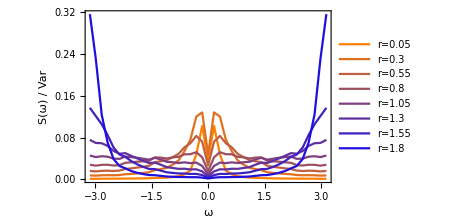

```mathematica
plotPspec=ListLinePlot[specPlotData,
PlotRange->All,
ImageSize->350,
PlotStyle->cols,
Frame->True,
LabelStyle->12,
FrameLabel->{{"S(ω) / Var",""},{"ω",""}},
PlotLegends->Placed[legend,Scaled[{0.75,0.63}]]]
```

```mathematica
(* Export figure *)
Export["figures/pspec_ricker_std_stat.png",plotPspec,ImageResolution->200];
```

## Plots of EWS against r

```mathematica
(* Columns of DataFrame *)
dfEws[[1]]
```

{r,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

### Equilibrium value

```mathematica
indexEws=Position[dfEws[[1]],"State variable"][[1,1]];
```

```mathematica
col=TMBcolours[[1]];
```

```mathematica
rVals
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95}

```mathematica
ewsSeries=dfEws[[2;;,indexEws]];
```

```mathematica
powersRange=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange}],Table[Superscript["10",ToString[i]],{i,powersRange}]}];
```

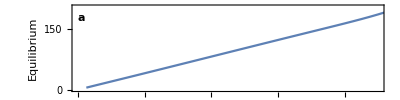

```mathematica
equiPlot=ListPlot[Transpose[{rVals,ewsSeries}],
LabelStyle->ls,
Joined->True,
PlotRange->{xRange,All},
PlotStyle->col,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Equilibrium",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["a",letls,Bold],labelPos]}
]
```

### Variance

```mathematica
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
col=TMBcolours[[1]];
```

```mathematica
rVals
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95}

```mathematica
ewsSeries=dfEws[[2;;,indexEws]];
```

```mathematica
powersRange=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange}],Table[Superscript["10",ToString[i]],{i,powersRange}]}];
```

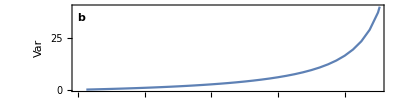

```mathematica
varPlot=ListPlot[Transpose[{rVals,ewsSeries}],
LabelStyle->ls,
Joined->True,
PlotRange->{xRange,{0,40}},
PlotStyle->col,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Var",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["b",letls,Bold],labelPos]}
]
```

### Coefficient of variation

```mathematica
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
col=TMBcolours[[1]];
```

```mathematica
rVals
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95}

```mathematica
ewsSeries=dfEws[[2;;,indexEws]];
```

```mathematica
powersRange=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange}],Table[Superscript["10",ToString[i]],{i,powersRange}]}];
```

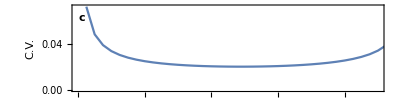

```mathematica
cvPlot=ListPlot[Transpose[{rVals,ewsSeries}],
LabelStyle->ls,
Joined->True,
PlotRange->{xRange,All},
PlotStyle->col,
Frame->{{True,True},{True,True}},
FrameLabel->{{"C.V.",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["c",letls,Bold],labelPos]}
]
```

### Autocorrelation

```mathematica
dfEws[[1]]
```

{r,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean}

```mathematica
indexEws=Position[dfEws[[1]],#][[1,1]]& /@{"Lag-1 AC","Lag-2 AC","Lag-3 AC"};
```

```mathematica
col=TMBcolours[[1;;3]];
```

```mathematica
ls
```

11

```mathematica
(* line legend *)
legend=LineLegend[col,Table["lag-"<>ToString[i],{i,{1,2,3}}],Spacings->{0,0},LabelStyle->ls-1]
```

```mathematica
rVals
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95}

```mathematica
ewsSeries=dfEws[[2;;,indexEws]]//Transpose;
```

```mathematica
powersRange=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange}],Table[Superscript["10",ToString[i]],{i,powersRange}]}];
```

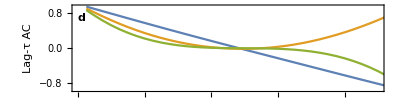

```mathematica
acPlot=ListPlot[Transpose[{rVals,ewsSeries[[#]]}]&/@{1,2,3},
LabelStyle->ls,
Joined->True,
PlotRange->{xRange,All},
PlotStyle->col,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Lag-τ AC",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
PlotLegends->Placed[legend,Scaled[{0.1,0.25}]],
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["d",letls,Bold],labelPos]}
]
```

### Smax/Var

```mathematica
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
col=TMBcolours[[1]];
```

```mathematica
rVals
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95}

```mathematica
ewsSeries=dfEws[[2;;,indexEws]];
```

```mathematica
powersRange=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange}],Table[Superscript["10",ToString[i]],{i,powersRange}]}];
```

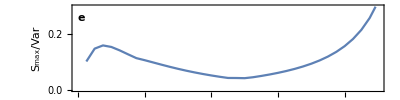

```mathematica
smaxVarPlot=ListPlot[Transpose[{rVals,ewsSeries}],
LabelStyle->ls,
Joined->True,
PlotRange->{xRange,{0,0.3}},
PlotStyle->col,
Frame->{{True,True},{True,True}},
FrameLabel->{{"S_max/Var",""},{"",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{FontOpacity->0,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->padding,
Epilog->{Directive[{Black}],Text[Style["e",letls,Bold],labelPos]}
]
```

### Skewness

```mathematica
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
col=TMBcolours[[1]];
```

```mathematica
rVals
```

{0.05,0.1,0.15,0.2,0.25,0.3,0.35,0.4,0.45,0.5,0.55,0.6,0.65,0.7,0.75,0.8,0.85,0.9,0.95,1.,1.05,1.1,1.15,1.2,1.25,1.3,1.35,1.4,1.45,1.5,1.55,1.6,1.65,1.7,1.75,1.8,1.85,1.9,1.95}

```mathematica
ewsSeries=dfEws[[2;;,indexEws]];
```

```mathematica
powersRange=Range[-4,4,2];
yTicksX=Transpose[{Table[10^i,{i,powersRange}],Table[Superscript["10",ToString[i]],{i,powersRange}]}];
```

```mathematica
padding
```

{{60,60},{20,20}}

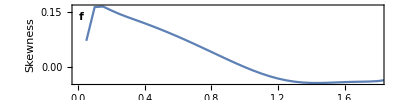

```mathematica
skewPlot=ListPlot[Transpose[{rVals,ewsSeries}],
LabelStyle->ls,
Joined->True,
PlotRange->{xRange,All},
PlotStyle->col,
Frame->{{True,True},{True,True}},
FrameLabel->{{"Skewness",""},{"r",""}},
FrameTicks->{{Automatic,None},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
ImagePadding->{{60,60},{50,20}},
Epilog->{Directive[{Black}],Text[Style["f",letls,Bold],labelPos]}
]
```

## Grid all plots together

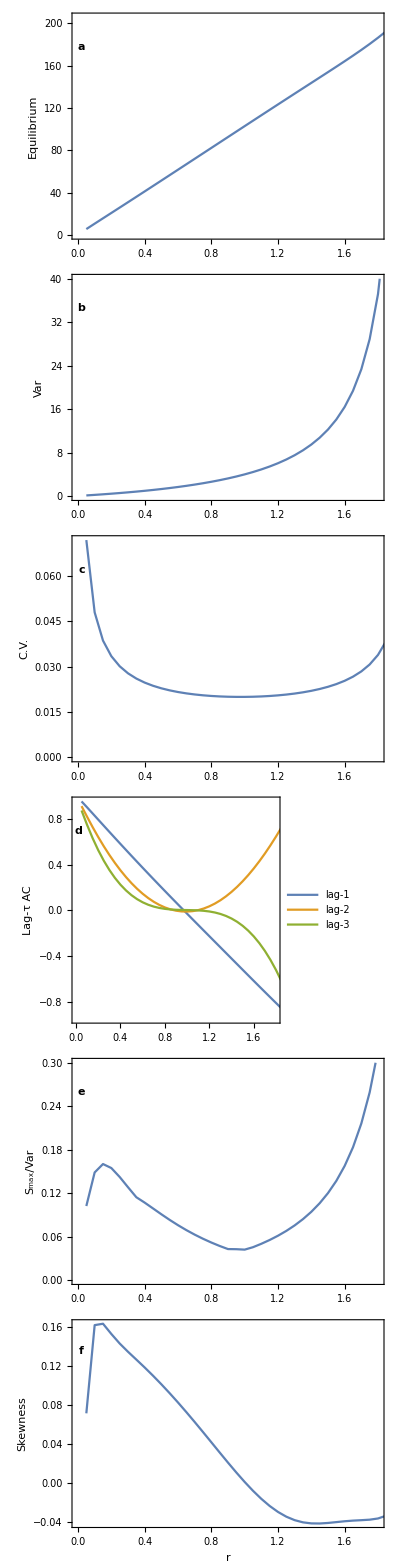

```mathematica
plotTemp=Grid[{{equiPlot},{varPlot},{cvPlot},{acPlot},{smaxVarPlot},{skewPlot}},Spacings->{0,-2.5}]
```

```mathematica
Export["figures/ews_stat_ricker_std.png",plotTemp,ImageResolution->200];
```